```mathematica
(h*OR/2)*Integrate[Sqrt[2/a]*Sqrt[2/R]*Sin[k*r]*Exp[-r/a],{r,0,Infinity}]
```

ConditionalExpression[(√(1/a) h k OR √(1/R))/(1/a^2+k^2), Re[1/a]>Abs[Im[k]]]

```mathematica
(√(1/a) h k OR √(1/R))/(1/a^2+k^2)//FullSimplify
```

(√(1/a) h k OR √(1/R))/(1/a^2+k^2)

```mathematica
Solve[D[k/(1/a^2 +k^2),k]==0,k]//FullSimplify
```

{{k→-1/a},{k→1/a}}

```mathematica
(1/a)/(1/a^2+1/a^2)
```

a/2

```mathematica
Series[(√(1/a) h k OR √(1/R))/(1/a^2+k^2),{k,0,2}]//FullSimplify
```

(h OR √(1/R) k)/(1/a)^(3/2)+O[k]^3

```mathematica
Series[(√(1/a) h (1/x) OR √(1/R))/(1/a^2+(1/x)^2),{x,0,2}]//FullSimplify
```

√(1/a) h OR √(1/R) x+O[x]^3

```mathematica
Manipulate[Plot[k/(1/a^2+k^2),{k,0,10}],{a,0.1,10}]
```

```mathematica
FullSimplify[(2*Pi/h)*(h^2*ΩR^2/(a*R))*(R/Pi)*Integrate[(k/(1/a^2+k^2))^2 * DiracDelta[En - h^2*k^2/(2m)],{k,0,Infinity}],Assumptions->{m>0,h>0,En>0,a>0}]
```

(2 √2 a^3 h^2 √(En m^3) ΩR^2)/((h^2+2 a^2 En m)^2)

```mathematica
2 √2 a^3 h^2 √(En m^3) ΩR^2*(1/(2*a^2*m))^2//FullSimplify
```

(En h^2 m ΩR^2)/(√2 a √(En m^3))

```mathematica
(En h^2 m ΩR^2)/(√2 a √(En m^3))/.{m->-h^2/(2*a^2*Em)}//FullSimplify
```

(a^3 Em^2 √(-(En h^6)/(a^6 Em^3)) ΩR^2)/h^2

```mathematica
FullSimplify[(a^3 Em^2 √(-(En h^6)/(a^6 Em^3)) ΩR^2)/h^2,Assumptions->{Em<0,h>0,a>0,En>0}]
```

Em^2 √(-En/Em^3) h ΩR^2

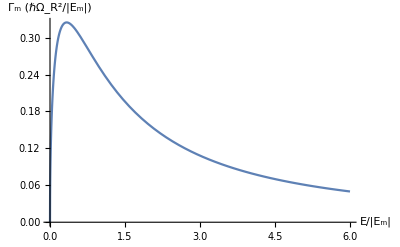

```mathematica
Plot[Sqrt[x]/(x+1)^2,{x,0,6},AxesLabel->{"E/|E_m|","Γ_m (ℏΩ_R^2/|E_m|)"},PlotRange->Full]
```

```mathematica
Series[h*OR^2*Sqrt[-e*Em]/(e-Em)^2,{e,0,2}]
```

(√-Em h OR^2 √e)/Em^2+(2 √-Em h OR^2 e^(3/2))/Em^3+O[e]^(5/2)

```mathematica
Integrate[(2/(Pi*h))*h*OR^2*Sqrt[e*EM]/(e+EM)^2,{e,0,Infinity}]
```

ConditionalExpression[OR^2, ]

```mathematica
(1/(2*Pi))*(h*OR^2)*Integrate[Sqrt[e*EM]/((e+EM)^2*(En-e)),{e,0,Infinity},PrincipalValue->True]
```

ConditionalExpression[-((EM-En) h OR^2)/(4 (EM+En)^2), Im[En]==0&&(Im[EM]≠0||Re[EM]≥0)&&Re[En]>0]

```mathematica
(1/(2*Pi))*(h*OR^2)*Integrate[Sqrt[-e*EM]/((-e+EM)^2*(En-e)),{e,0,Infinity},PrincipalValue->True]
```

ConditionalExpression[((EM+En) h OR^2)/(4 (EM-En)^2), Im[En]==0&&(Im[EM]≠0||Re[EM]≤0)&&Re[En]>0]

```mathematica
FullSimplify[Integrate[Sqrt[t]/((1+t)^2*(a-t)),{t,-Infinity,Infinity},PrincipalValue->True],Assumptions->{a<0}]
```

ConditionalExpression[((-1+√-a+a) π)/(1+a)^2, a>-1]

```mathematica
deltatest[x_]:=HeavisideTheta[x]*(x-1)/(4(x+1)^2)+HeavisideTheta[-x]*-1/(4(1+Sqrt[-x])^2);
```

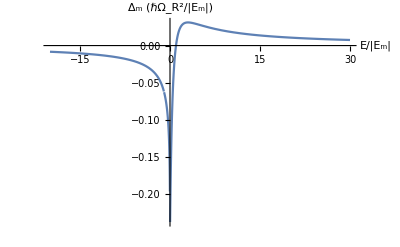

```mathematica
Plot[deltatest[x],{x,-20,30},AxesLabel->{"E/|E_m|","Δ_m (ℏΩ_R^2/|E_m|)"},PlotRange->Full]
```

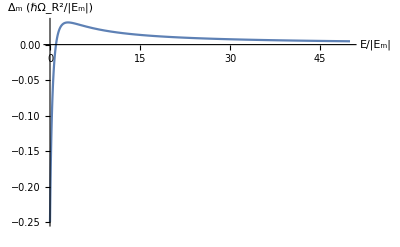

```mathematica
Plot[(x-1)/(4(x+1)^2),{x,0,50},AxesLabel->{"E/|E_m|","Δ_m (ℏΩ_R^2/|E_m|)"},PlotRange->Full]
```

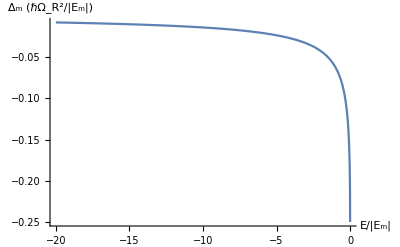

```mathematica
Plot[-1/(4(1+Sqrt[-x])^2),{x,0,-20},AxesLabel->{"E/|E_m|","Δ_m (ℏΩ_R^2/|E_m|)"},PlotRange->Full]
```

```mathematica
U[x_,y_,z_,xi_]:=((xi^2/2 * Sqrt[x]/(x+1)^2 + z)/((x-y-xi^2/4 * (x-1)/(x+1)^2)^2 + (xi^2/2 * Sqrt[x]/(x+1)^2 + z)^2 ))*HeavisideTheta[x]+
(z/( (x-y-xi^2/4 * (-1)/(1+Sqrt[-x])^2)^2 + z^2))*HeavisideTheta[-x];
```

```mathematica
DensityPlot[U[x,y,0.01,20],{y,-10,30},{x,0,30},PlotRange->Full,PlotPoints->300,FrameLabel->{"δ/|E_m|","E/|E_m|"}]
```

-Graphics-

```mathematica
DensityPlot[U[x,y,0.01,20],{y,-10,30},{x,-10,0},PlotRange->Full,PlotPoints->300,FrameLabel->{"δ/|E_m|","E/|E_m|"},PlotRange->All]
```

-Graphics-

```mathematica
delta[x_]:=HeavisideTheta[x]*(x-1)/(x+1)^2 + HeavisideTheta[-x]*(-1)/(1+Sqrt[-x])^2;
```

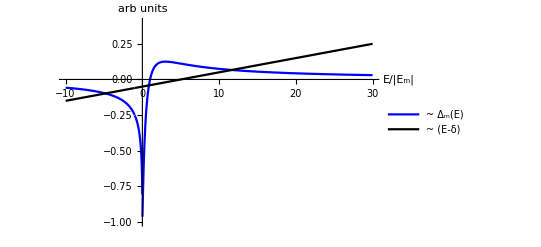

```mathematica
p1=Plot[{delta[x],(x-5)/10^2},{x,-10,30},PlotStyle->{Blue,Black},PlotLegends->{"~ Δ_m(E)","~ (E-δ)"},PlotRange->{-1,0.4},AxesLabel->{"E/|E_m|","arb units"}]
```

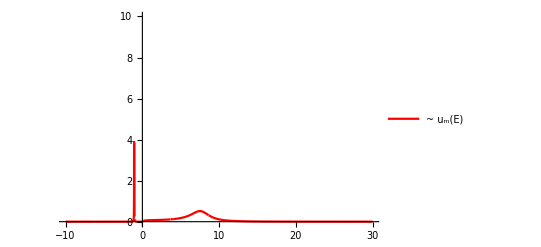

```mathematica
p3=Plot[U[x,5,0.01,10],{x,-10,30},PlotStyle->{Red},PlotLegends->{"~ u_m(E)"},PlotRange->{-0.01, 10}]
```

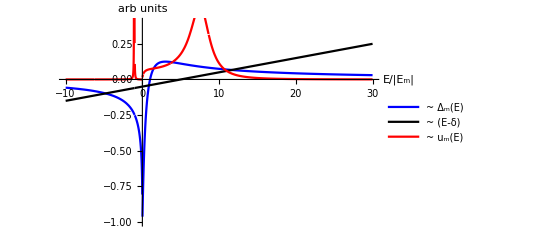

```mathematica
Show[p1,p3]
```

```mathematica
Integrate[Sqrt[e]*Exp[-I*e*t/h],{e,0,h/t}]//FullSimplify
```

-(h^2 √π √((ⅈ t)/h))/(2 t^2)-(h/t)^(3/2) ExpIntegralE[-1/2,ⅈ]

```mathematica
N[ExpIntegralE[-1/2,ⅈ]]
```

-1.15786-0.262435 ⅈ

```mathematica
(*Part f*)
```

```mathematica
Manipulate[Plot[U[x,0.5,0.01,xi],{x,-200,200},PlotStyle->{Red},PlotLegends->{"~ u_m(E)"},PlotRange->{-0.01, 0.08}],{xi,0,300}]
```

```mathematica
Solve[x-y-xi^2/4 * (-1)/(1+Sqrt[-x])^2==0,xi]//FullSimplify
```

{{xi→-2 (1+√-x) √(-x+y)},{xi→2 (1+√-x) √(-x+y)}}

```mathematica
Y[y_]:=HeavisideTheta[-y] /(1+Sqrt[-y])^2+
 HeavisideTheta[y]*(1-y)/(1+y)^2;
```

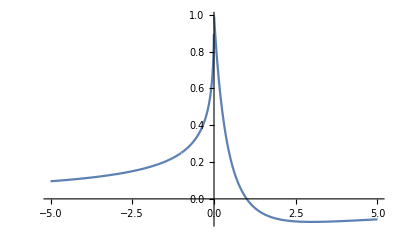

```mathematica
Plot[Y[y],{y,-5,5}]
```

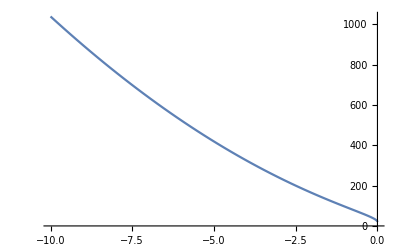

```mathematica
Plot[4(-x+5)*(1+Sqrt[-x])^2,{x,-10,0},PlotRange->All]
```

```mathematica
Integrate[h*OR^2*Sqrt[e*EM]/(e+EM)^2*(1/e),{e,0,Infinity}]/OR^2
```

ConditionalExpression[(h π)/(2 EM), Im[EM]≠0||Re[EM]≥0]

```mathematica
Solve[e==h^2*ORC^2/(4*EM) + h^2*OR^2/(4*e),e]//FullSimplify
```

{{e→(h^2 ORC^2-√(16 EM^2 h^2 OR^2+h^4 ORC^4))/(8 EM)},{e→(h^2 ORC^2+√(16 EM^2 h^2 OR^2+h^4 ORC^4))/(8 EM)}}

```mathematica
U[t_]:=Integrate[Exp[-I*e*t]*(DiracDelta[e+1]+(3)/((e-1)^2+3^2/4)),{e,-Infinity,Infinity}]
```

```mathematica
Plot[Abs[U[t]]^2,{t,0,20}]
```

$Aborted

```mathematica
Integrate[Exp[-I*e*t]*(DiracDelta[e+1]),{e,-Infinity,Infinity}]
```

ⅇ^(ⅈ t)

```mathematica
Integrate[Exp[-I*e*t]*(DiracDelta[e+1]),{e,-Infinity,Infinity}]
```

ⅇ^(ⅈ t)

```mathematica
U[t_]:=NIntegrate[(1/(2*Pi))*0.2/((e-1)^2+0.2^2/4)*Exp[-I*e*t],{e,-20,20}]+Exp[I*t];
```

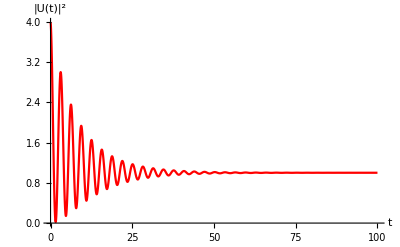

```mathematica
Plot[Abs[U[t]]^2,{t,0,100},PlotRange->All,AxesLabel->{"t","|U(t)|^2"},PlotStyle->Red]
```

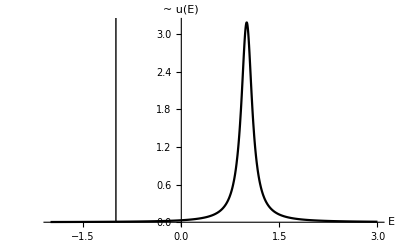

```mathematica
Plot[DiracDelta[x+1]+(1/(2*Pi))*0.2/((x-1)^2+0.2^2/4),{x,-2,3},PlotRange->All,Epilog->Line[{{-1,0},{-1,7}}],PlotStyle->Black,AxesLabel->{"E","~ u(E)"}]
```